```mathematica
a=2;
b=2;
α=a/b;
ρ=7850;
h=0.01;
EM=2.1*10^11;
ν=0.3;
K=(EM*h^3)/(12*(1-ν^2));
m=1;
n=1;

p=(m*π)/α
(*λ((ρ*h*a^4)/(α^4*K))^(1/4)*)
β1=√(p^2+λ^2);
β2=√(λ^2-p^2)

GL=Tanh[β1]/Tan[β2]-β1/β2==0
(*NSolve[GL,λ]*)
Erg=FindRoot[GL,{λ,5}]
λ=λ/.Erg;
```

π

√(-π^2+λ^2)

-(√(π^2+λ^2))/(√(-π^2+λ^2))+Cot[√(-π^2+λ^2)] Tanh[√(π^2+λ^2)]==0

{λ→4.86275}

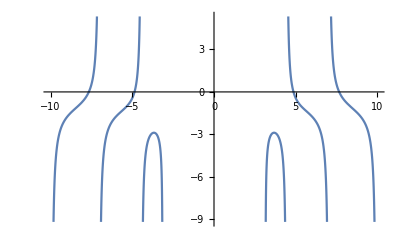

```mathematica
Plot[Tanh[β1]/Tan[β2]-β1/β2,{λ,-10,10}]
```

```mathematica
(β1^2+β2^2)/2*Sqrt[(α^4*K)/(ρ*h*a^4)]
```

92.5267